# Mathematica for Bioinformatics

by George I. Mias, PhD
["http://georgemias.org"](http://georgemias.org)

## Chapter 10: Networks

## Introduction to Graphs

### Vertices and Edges



```mathematica
Graph[{1<->2}]
```

```mathematica
Graph[{1<->2},PlotTheme->"ClassicDiagram"]
```

-Graphics-

```mathematica
Graph[{1->2},PlotTheme->"ClassicDiagram"]
```

-Graphics-

```mathematica
simpleGraphExample=Graph[
{1->2,2<->3,3-> 4,2-> 4,2-> 5,
3-> 5,5<->1},PlotTheme->"ClassicDiagram"]
```

-Graphics-

```mathematica
simpleGraphExample7=Graph[{1,2,3,4,5,6,7},
{1->2,2<->3,3-> 4,2-> 4,2-> 5,3-> 5,5<->1},
PlotTheme->"ClassicDiagram"]
```

-Graphics-

```mathematica
SystemOpen["paclet:example/VisualizeEulerianCycles"] (* the figure is available in the Documentation Center*)
```

```mathematica
sevenBridges=Graph[{UndirectedEdge[1,2],
 UndirectedEdge[1,2], UndirectedEdge[2, 3],
UndirectedEdge[2, 3], UndirectedEdge[2,4],
 UndirectedEdge[3,4],UndirectedEdge[1, 4]},
PlotTheme->"ClassicDiagram"]
```

-Graphics-

```mathematica
EulerianGraphQ[sevenBridges]
```

False

## Basic Graph Construction

### Entering a Graph

```mathematica
vertexLabels=#-> Style[Subscript[ "V",
ToString[#]],FontFamily->"Arial",Bold]&/@Range[7]
```

{1→V_1,2→V_2,3→V_3,4→V_4,5→V_5,6→V_6,7→V_7}

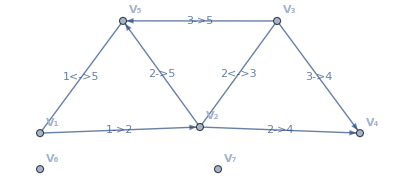

```mathematica
simpleGraphExample7Labeled=Graph[Range[7],
{1->2,2<->3,3-> 4,2-> 4,2-> 5,3-> 5,5<->1},
VertexLabels-> vertexLabels,
EdgeLabels->"Name"]
```

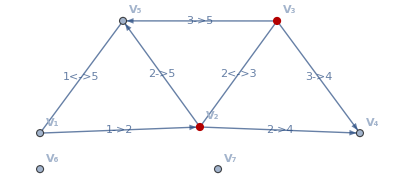

```mathematica
HighlightGraph[simpleGraphExample7Labeled,{2,3}]
```

```mathematica
verticesCentralDogma={"DNA","mRNA","Protein"};
edgesCentralDogma={DirectedEdge["DNA","mRNA"],
DirectedEdge["mRNA","Protein"]};
edgeLabelsCentralDogma={DirectedEdge["DNA","mRNA"]->
Labeled["DNA to mRNA","Transcription"],
DirectedEdge["mRNA","Protein"]-> 
Labeled["mRNA to Protein", "Translation"]};
```

```mathematica
centralDogmaGraph=Graph[verticesCentralDogma,
edgesCentralDogma,
VertexSize-> 0.3,
PlotTheme->"ClassicDiagram",
EdgeLabels->edgeLabelsCentralDogma]
```

-Graphics-

```mathematica
VertexList[centralDogmaGraph]
```

{DNA,mRNA,Protein}

```mathematica
VertexIndex[centralDogmaGraph,"Protein"]
```

3

```mathematica
EdgeList[centralDogmaGraph]
```

{DNA->mRNA,mRNA->Protein}

```mathematica
EdgeIndex[centralDogmaGraph,"mRNA"->"Protein"]
```

2

```mathematica
VertexIndex[centralDogmaGraph,"DNA"]
```

1

```mathematica
EdgeDelete[simpleGraphExample7,2->  5]
(*Can also input as 
EdgeDelete[simpleGraphExample,DirectedEdge[2,5]]*)
```

-Graphics-

```mathematica
EdgeAdd[simpleGraphExample7,1<->3]
```

-Graphics-

```mathematica
VertexDelete[simpleGraphExample7,1]
```

-Graphics-

```mathematica
VertexAdd[simpleGraphExample7,6]
```

-Graphics-

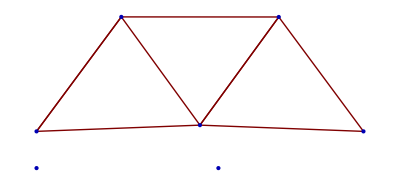

```mathematica
graphPlot=GraphPlot[simpleGraphExample7]
```

```mathematica
Head[graphPlot]
```

Graphics

```mathematica
Head[simpleGraphExample]
```

Graph

### Defining Weighted Graphs

```mathematica
edgeWeights= {2,3,1,6,1,2,1};
```

```mathematica
simpleGraphExampleWeightedEdges=
Graph[{1->2,2<->3,3-> 4,2-> 4,
2-> 5,3-> 5,5<->1},
EdgeWeight-> edgeWeights,
PlotTheme->"ClassicDiagram"];simpleGraphExampleWeightedEdges
```

-Graphics-

```mathematica
Graph[{1->2,2<->3,3-> 4,2-> 4,2-> 5,
3-> 5,5<->1},
EdgeWeight-> edgeWeights,
PlotTheme->"ClassicDiagram",
EdgeLabels->"EdgeWeight"]
```

-Graphics-

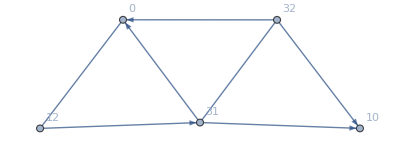

```mathematica
simpleGraphExampleWeightedVertices=
Graph[{1->2,2<->3,3-> 4,2-> 4,
2-> 5,3-> 5,5<->1},
VertexWeight-> {12,31,32,10,0},
VertexLabels-> "VertexWeight"]
```

## Basic Graph Properties

### Degree

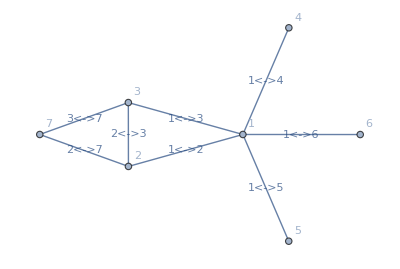

```mathematica
graphExample7VerticesEdges=
{1<-> 2,2<->3,3<->1,4<-> 1,5<-> 1,6<-> 1,
7<-> 2,7<-> 3};
graphExample7Vertices=
Graph[graphExample7VerticesEdges,
VertexLabels-> "Name",
EdgeLabels->"Name"]
```

```mathematica
VertexDegree[graphExample7Vertices]
```

{5,3,3,1,1,1,2}

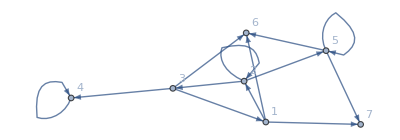

```mathematica
graphExampleLoopsDirectedEdges=
{1->2,2->3,2->2,3->1,3->4,4->4,2->5,
1->6,3->6,5->6,1->7,5->7,5->5};
graphExampleLoopsDirected=
Graph[graphExampleLoopsDirectedEdges,
VertexLabels-> "Name"]
```

```mathematica
VertexOutDegree[graphExampleLoopsDirected]
```

{3,3,3,1,3,0,0}

```mathematica
VertexInDegree[graphExampleLoopsDirected]
```

{1,2,1,2,2,3,2}

```mathematica
VertexDegree[graphExampleLoopsDirected]
```

{4,5,4,3,5,3,2}

### Adjacency Matrix

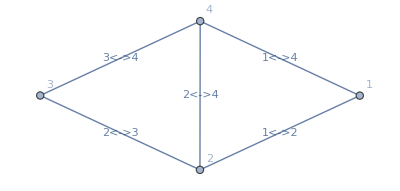

```mathematica
graphSimple=Graph[{1, 2, 3, 4},
 {UndirectedEdge[1, 2], UndirectedEdge[2, 3],
 UndirectedEdge[2, 4], UndirectedEdge[3, 4],
 UndirectedEdge[1, 4]},
VertexLabels->"Name",
EdgeLabels->"Name"]
```

```mathematica
adjGraphSimple=AdjacencyMatrix[graphSimple];
```

```mathematica
Head[adjGraphSimple]
```

SparseArray

```mathematica
adjGraphSimple["Properties"]
```

{AdjacencyLists,Background,ColumnIndices,Density,MatrixColumns,NonzeroValues,PatternArray,Properties,RowPointers}

```mathematica
adjGraphSimple//MatrixForm
```

(0 | 1 | 0 | 1
1 | 0 | 1 | 1
0 | 1 | 0 | 1
1 | 1 | 1 | 0)

```mathematica
adjSevenBridges=AdjacencyMatrix[sevenBridges];
adjSevenBridges//MatrixForm
```

(0 | 2 | 0 | 1
2 | 0 | 2 | 1
0 | 2 | 0 | 1
1 | 1 | 1 | 0)

```mathematica
AdjacencyMatrix[Graph[graphExampleLoopsDirected]]//MatrixForm
```

(0 | 1 | 0 | 0 | 0 | 1 | 1
0 | 1 | 1 | 0 | 1 | 0 | 0
1 | 0 | 0 | 1 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0)

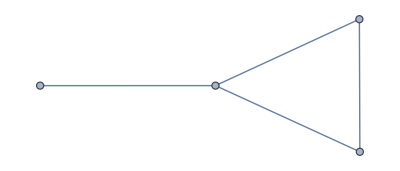

```mathematica
AdjacencyGraph[{{0,1,0,1},{1,0,1,1},
{0,1,0,0},{1,1,0,0}}]
```

### Weighted Adjacency Matrix

```mathematica
exampleWeightedAdjacencyMatrix=
WeightedAdjacencyMatrix[simpleGraphExampleWeightedEdges]//MatrixForm
```

(0 | 2 | 0 | 0 | 1
0 | 0 | 3 | 6 | 1
0 | 3 | 0 | 1 | 2
0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0)

```mathematica
AdjacencyMatrix[
simpleGraphExampleWeightedEdges]//
MatrixForm
```

(0 | 1 | 0 | 0 | 1
0 | 0 | 1 | 1 | 1
0 | 1 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0)

## Some More Definitions

### Walks and Paths

Walk: a walk on a graph is a sequence of vertices, {v_1,v_2,...,v_n} so that  all edges connecting sequential elements in the list are included.

Path: a path is a walk in which the list of vertices does not include duplicates - i.e. no vertex is visited twice.  In a connected graph any vertex in the graph has a path to any other vertex in the graph. A disconnected graph is a graph that is not connected (and will thus have graph parts disconnected from the rest)

Trail: a trail is a walk in which the edges are distinct (but the vertices do not have to be)

Cycle: a cycle is a path with an additional edge connecting the last to the first vertex (think of a circle closing on itself)

Geodesic: a geodesic is the shortest path that can be found connecting two vertices

Length: The length is defined in terms of the number of edges in any of the above.

```mathematica
shortestPath7Vertices=FindShortestPath[graphExample7Vertices,1,7]
```

{1,2,7}

```mathematica
shortestPathGraph=PathGraph[shortestPath7Vertices];
```

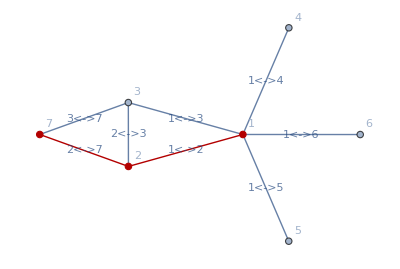

```mathematica
HighlightGraph[graphExample7Vertices,shortestPathGraph]
```

### Graph Geometry

Eccentricity: the eccentricity,ϵ of a vertex is the maximum shortest path between the given vertex and any other vertex. For any graph we can use the function VertexEccentricity[graph, vertex_i] to get he eccentricity. For example we extract all the eccentricities for thesevenBridges and simpleGraphExample graphs from above:

```mathematica
VertexEccentricity[sevenBridges,#]&/@VertexList[sevenBridges]
```

{2,1,2,1}

```mathematica
VertexEccentricity[graphExample7Vertices,#]&/@VertexList[graphExample7Vertices]
```

{2,2,2,3,3,3,3}

Graph Diameter: the graph diameter, d,  is the maximum eccentricity measured across all vertices of the graph. The set of all vertices with eccentricity equal to the diameter d is the periphery of the graph.

```mathematica
GraphDiameter[sevenBridges]
```

2

```mathematica
GraphDiameter[graphExample7Vertices]
```

3

Graph Radius: the graph radius, r,  is the minimum eccentricity measured across all vertices of the graph. Any vertex is called central if its eccentricity matches r, and the set of these central vertices is the center of the graph.

```mathematica
GraphRadius[sevenBridges]
```

1

```mathematica
GraphRadius[graphExample7Vertices]
```

2

### Centrality

Degree Centrality: For a given vertex, we can think of it as being important the higher its degree. DegreeCentrality can calculate the measure for all vertices in a graph:

```mathematica
DegreeCentrality[graphExample7Vertices]
```

{5,3,3,1,1,1,2}

Betweenness Centrality: We can calculate the betweenness centrality of an edge in a graph. This is defined as the number of shortest paths between the vertex pairs that include the edge.  It measures the numbers of vertex pair sets that essentially go through the edge to connect to each other. For our previous example we get:

```mathematica
BetweennessCentrality[graphExample7Vertices]
```

{12.,2.,2.,0.,0.,0.,0.}

```mathematica
scaledBetweenness=Rescale[BetweennessCentrality[graphExample7Vertices]]
```

{1.,0.166667,0.166667,0.,0.,0.,0.}

```mathematica
vertexListExample7=VertexList[graphExample7Vertices];
```

```mathematica
HighlightGraph[graphExample7Vertices,vertexListExample7,VertexSize-> Thread[vertexListExample7-> scaledBetweenness]]
```

-Graphics-

### Clustering Coefficient

#### Local Clustering Coefficient

```mathematica
localClusteringExample7=LocalClusteringCoefficient[graphExample7Vertices]
```

{1/10,2/3,2/3,0,0,0,1}

```mathematica
HighlightGraph[graphExample7Vertices,vertexListExample7,VertexSize-> Thread[vertexListExample7-> localClusteringExample7]]
```

-Graphics-

#### Global Clustering Coefficient

```mathematica
GlobalClusteringCoefficient[graphExample7Vertices]
```

6/17

## Graph Examples

### Empty Graphs

```mathematica
emptyGraphs=Graph[GraphData[{"Empty",#}],VertexSize-> Medium,PlotLabel->Style[Subscript["E",#],Italic,Bold]] &/@ Range[5];
```

```mathematica
gridGraphs[x_]:=Grid[{x},Dividers->Center,Frame-> True, FrameStyle->Directive[Dashing[4],Thickness[2],Opacity[0.3]]]
```

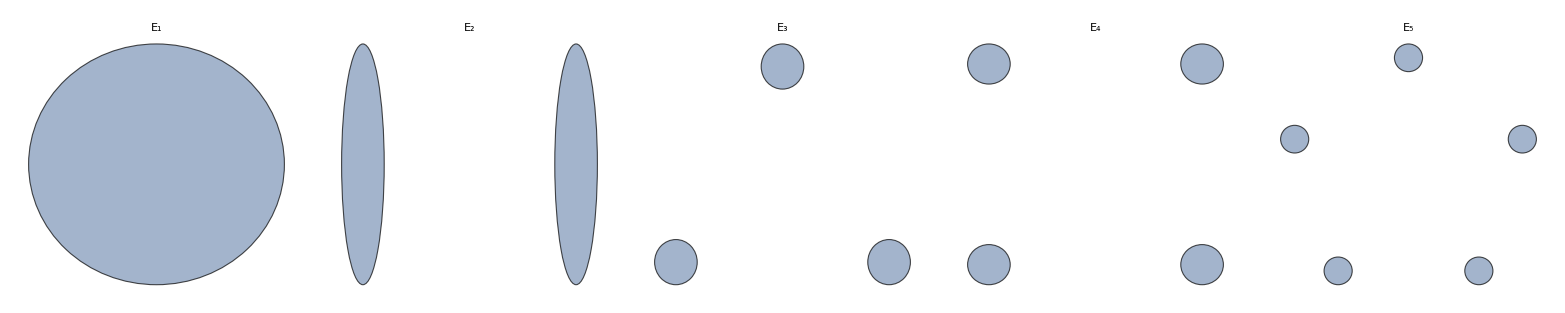

```mathematica
gridGraphs[emptyGraphs]
```

### Complete Graphs

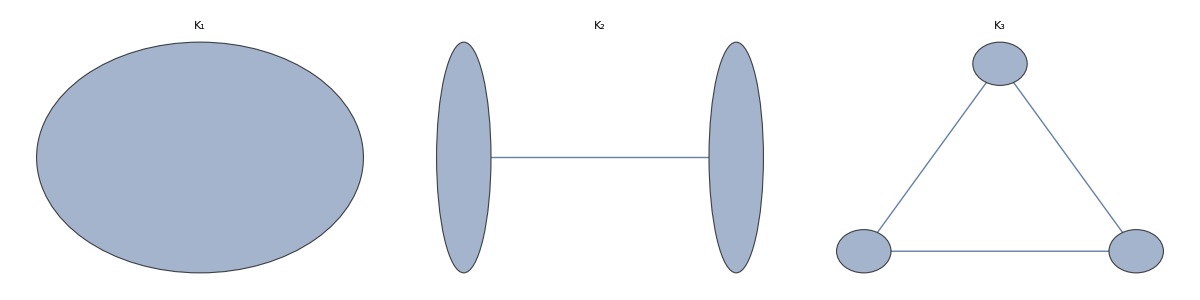

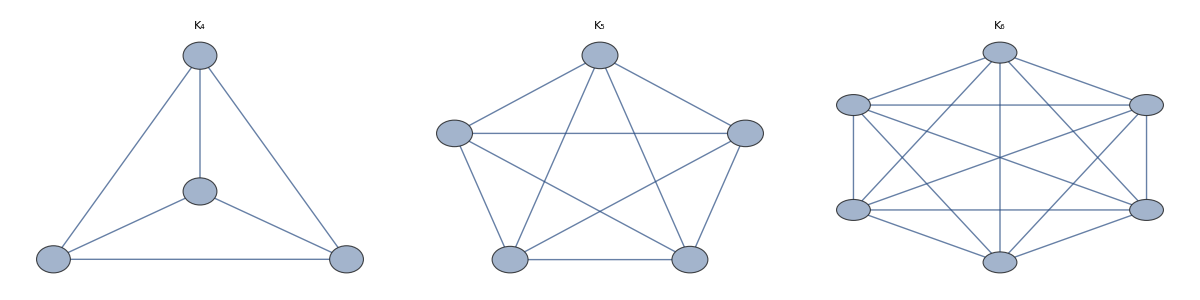

```mathematica
completeGraphs=CompleteGraph[#,
PlotLabel->
Style[Subscript["K",#],Italic,Bold],
VertexSize-> Medium,
EdgeStyle-> Automatic]&/@ Range[7];
gridGraphs[completeGraphs[[1;;3]]]
gridGraphs[completeGraphs[[4;;6]]]
```

```mathematica
MatrixForm@AdjacencyMatrix[#]&/@completeGraphs
```

{(0),(0 | 1
1 | 0),(0 | 1 | 1
1 | 0 | 1
1 | 1 | 0),(0 | 1 | 1 | 1
1 | 0 | 1 | 1
1 | 1 | 0 | 1
1 | 1 | 1 | 0),(0 | 1 | 1 | 1 | 1
1 | 0 | 1 | 1 | 1
1 | 1 | 0 | 1 | 1
1 | 1 | 1 | 0 | 1
1 | 1 | 1 | 1 | 0),(0 | 1 | 1 | 1 | 1 | 1
1 | 0 | 1 | 1 | 1 | 1
1 | 1 | 0 | 1 | 1 | 1
1 | 1 | 1 | 0 | 1 | 1
1 | 1 | 1 | 1 | 0 | 1
1 | 1 | 1 | 1 | 1 | 0),(0 | 1 | 1 | 1 | 1 | 1 | 1
1 | 0 | 1 | 1 | 1 | 1 | 1
1 | 1 | 0 | 1 | 1 | 1 | 1
1 | 1 | 1 | 0 | 1 | 1 | 1
1 | 1 | 1 | 1 | 0 | 1 | 1
1 | 1 | 1 | 1 | 1 | 0 | 1
1 | 1 | 1 | 1 | 1 | 1 | 0)}

```mathematica
BetweennessCentrality[#]&/@completeGraphs
```

{{0.},{0.,0.},{0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.}}

```mathematica
DegreeCentrality[#]&/@completeGraphs
```

{{0},{1,1},{2,2,2},{3,3,3,3},{4,4,4,4,4},{5,5,5,5,5,5},{6,6,6,6,6,6,6}}

### Regular Graphs.

```mathematica
Length@GraphData["Regular"]
```

5353

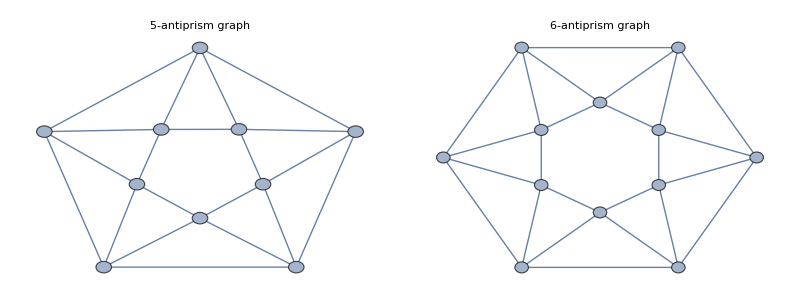

```mathematica
regularGraphs=Graph[GraphData[{"Antiprism",#}],
VertexSize-> Medium,
PlotLabel->
TextCell[GraphData[{"Antiprism",#},
"Name"]]] &/@ Range[5,6];
gridGraphs[regularGraphs]
```

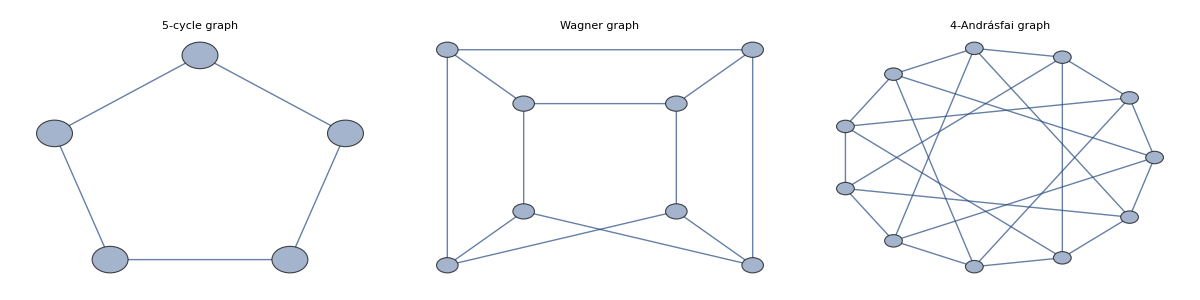

```mathematica
regularGraphs2=Graph[GraphData[{"Andrasfai",#}],
VertexSize-> Medium,
PlotLabel->TextCell[GraphData[{"Andrasfai",#},
"Name"]]] &/@ Range[2,4];
gridGraphs[regularGraphs2]
```

```mathematica
GraphData[{"Andrasfai",2},"Properties"]//Short
```

{Acyclic,AdjacencyMatrix,«458»,ZeroTwo}

```mathematica
GraphData[{"Andrasfai",2},{"VertexCount","EdgeCount","EdgeBetweennessCentralities","DegreeSequence"}]
```

{5,5,{6,6,6,6,6},{2,2,2,2,2}}

```mathematica
MatrixForm[#]&/@GraphData[{"Andrasfai",3},{"AdjacencyMatrix"}]
```

{(0 | 1 | 0 | 0 | 1 | 0 | 0 | 1
1 | 0 | 1 | 0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 1 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 1 | 0 | 0 | 1
1 | 0 | 0 | 1 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 1 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0 | 1 | 0 | 1
1 | 0 | 0 | 1 | 0 | 0 | 1 | 0)}

### Cycle Graphs

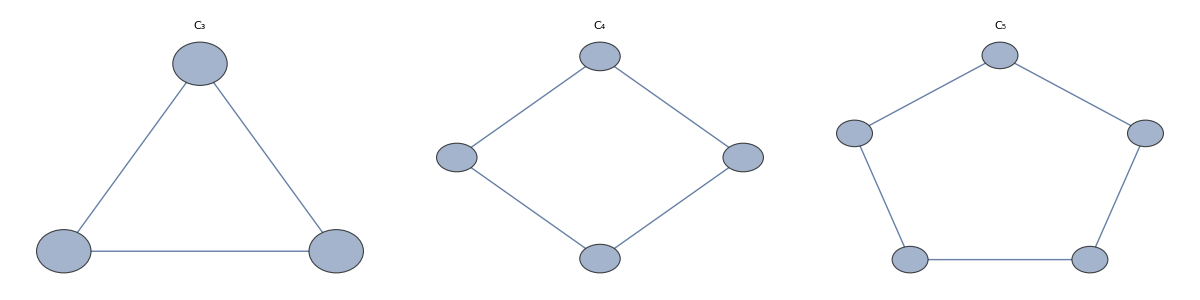

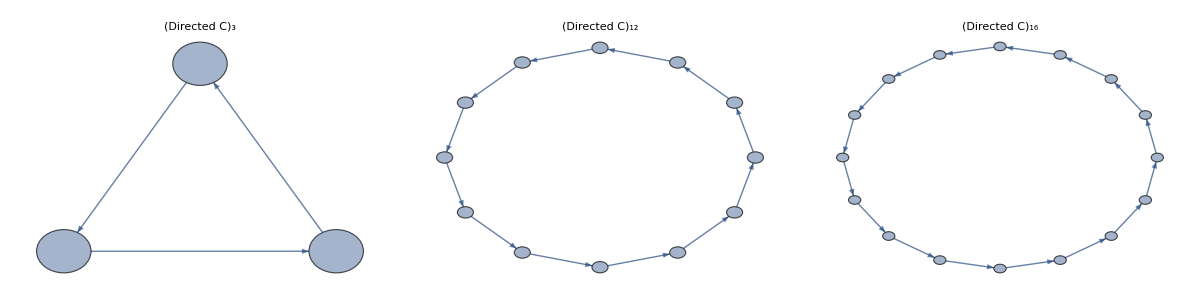

```mathematica
cycleGraphs={CycleGraph[#,VertexSize-> Medium,
PlotLabel->
Style[Subscript["C",#],Italic,Bold]] &/@
 Range[3,5],CycleGraph[#,VertexSize-> Medium,
PlotLabel->
Style[Subscript["Directed C",#],Italic,Bold],
DirectedEdges->True]&/@ {3,12,16} };
gridGraphs[cycleGraphs[[1]]]
gridGraphs[cycleGraphs[[2]]]
```

```mathematica
(Subscript["C",#]->MatrixForm[ AdjacencyMatrix[CycleGraph[#]]]&/@{3,5,10})
```

{C_3→(0 | 1 | 1
1 | 0 | 1
1 | 1 | 0),C_5→(0 | 1 | 0 | 0 | 1
1 | 0 | 1 | 0 | 0
0 | 1 | 0 | 1 | 0
0 | 0 | 1 | 0 | 1
1 | 0 | 0 | 1 | 0),C_10→(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)}

### Trees

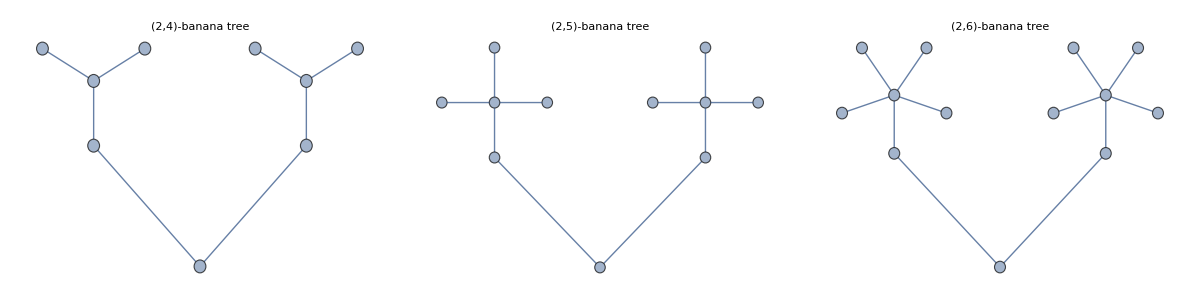

```mathematica
treeGraphs=Graph[
GraphData[{"BananaTree",{2,#}}],
VertexSize-> Medium,PlotLabel->
TextCell[GraphData[{"BananaTree",{2,#}},
"Name"]]] &/@ Range[4,6];
gridGraphs[treeGraphs]
```

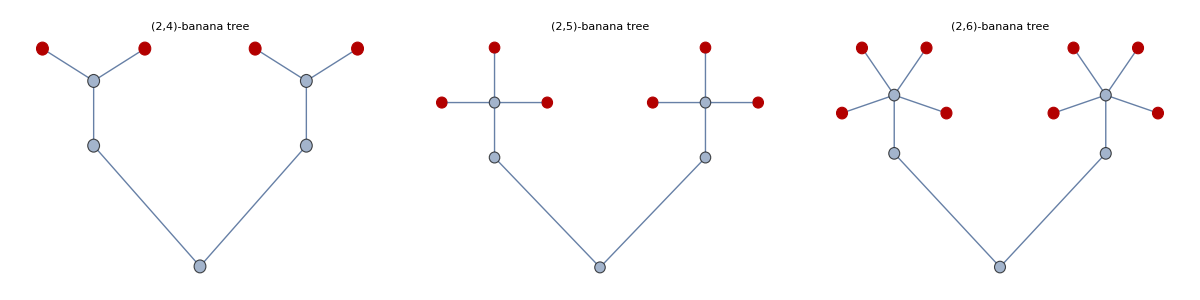

```mathematica
gridGraphs[HighlightGraph[#,GraphPeriphery[#]]&/@(treeGraphs)]
```

### Bipartite Graphs

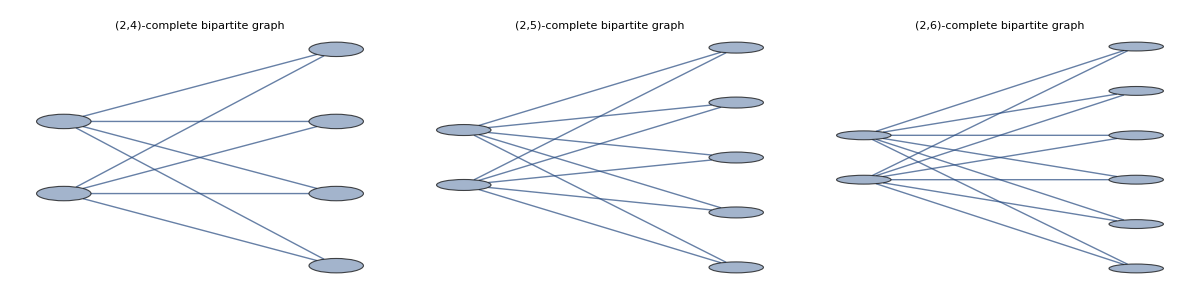

```mathematica
bipartiteGraphs=Graph[
GraphData[{"CompleteBipartite",{2,#}}],
VertexSize-> Medium,
PlotLabel->
TextCell[GraphData[{"CompleteBipartite",
{2,#}},"Name"]]] &/@ Range[4,6];
gridGraphs[bipartiteGraphs]
```

## Isomorphisms

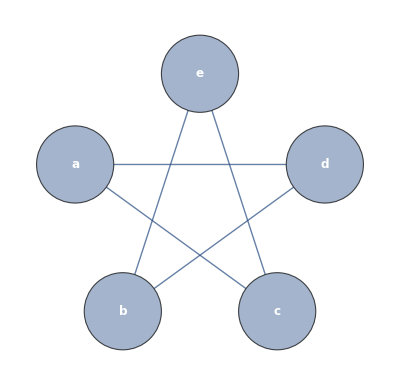
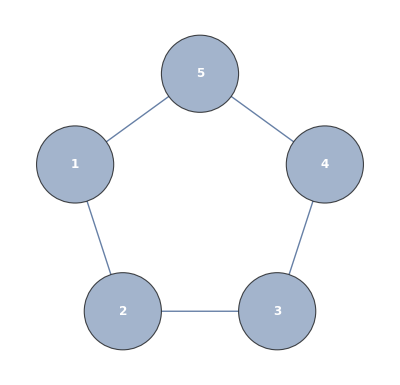
Graph1:-Graphics-Graph2:-Graphics-

```mathematica
graph1=Graph[
{"a","b","c","d","e"},
{"a"<-> "c","c"<->"e","e"<->"b","b"<->"d",
"d"<->"a"},
VertexSize->0.5,
VertexLabels-> Placed["Name",Center],
VertexLabelStyle->Directive[Bold,White,12],
VertexStyle->Thread[{"a","b","c","d","e"}->
{Red,Blue,Magenta,Orange,Purple}]];
graph2=CycleGraph[5,VertexSize->0.5,
VertexLabels-> Placed["Name",Center],VertexLabelStyle->Directive[Bold,White,12]];
Row[{"Graph1:",graph1,Spacer[40],
"Graph2:", graph2}]
```

```mathematica
IsomorphicGraphQ[graph1,graph2]
```

True

```mathematica
isomorphismG1G2=First@FindGraphIsomorphism[graph1,graph2]
```

<|a→1,b→3,c→5,d→2,e→4|>

```mathematica
Row@{graph1,Spacer[20],
Style[Column@Normal[isomorphismG1G2],
16,FontFamily->"Arial"],Spacer[20],
HighlightGraph[graph2, 
Style[isomorphismG1G2[#],
PropertyValue[{graph1,#},
VertexStyle]]&/@
VertexList[graph1]]}//TableForm
```

-Graphics-a→1
b→3
c→5
d→2
e→4-Graphics-

## Random Graphs

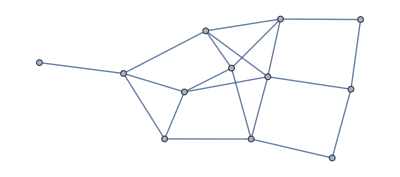

```mathematica
SeedRandom[7777];
RandomGraph[{12,20}]
```

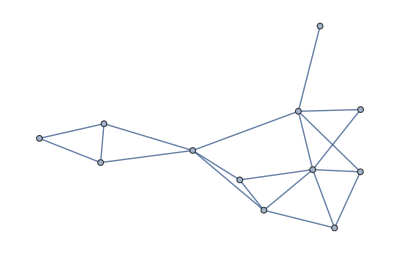
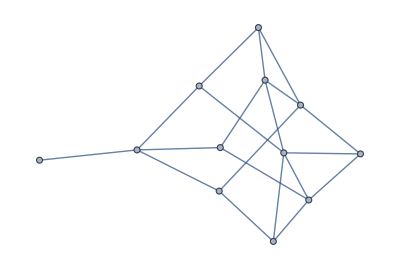
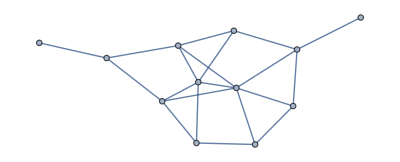
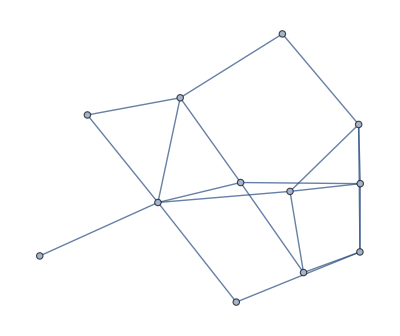
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
SeedRandom[7777];
RandomGraph[{12,20},5]
```

### Barabasi Albert Distribution

```mathematica
SeedRandom[7777];
barabasiAlbertRandomGraph=RandomGraph[BarabasiAlbertGraphDistribution[10^4,3]];
```

```mathematica
empiricalDistributionBarabasiAlbert=EmpiricalDistribution[VertexDegree[barabasiAlbertRandomGraph]];
```

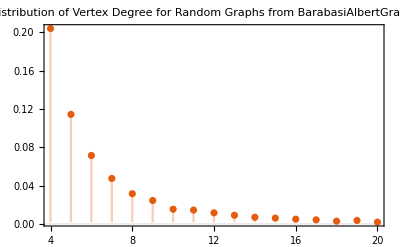

```mathematica
DiscretePlot[
PDF[empiricalDistributionBarabasiAlbert,i],
{i,4,20},
PlotRange-> 
All,PlotTheme-> "Scientific",PlotLabel->
"PDF of Empirical Distribution 
of Vertex Degree for Random Graphs 
from BarabasiAlbertGraphDistribution[10^4,3]]"]
```

### Watts Strogatz

```mathematica
?WattsStrogatzGraphDistribution
```

WattsStrogatzGraphDistribution[n,p] represents the Watts–Strogatz graph distribution for n-vertex graphs with rewiring probability p.
WattsStrogatzGraphDistribution[n,p,k] represents the Watts–Strogatz graph distribution for n-vertex graphs with rewiring probability p starting from a 2k-regular graph.

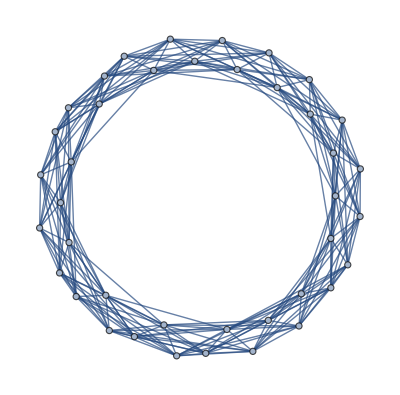
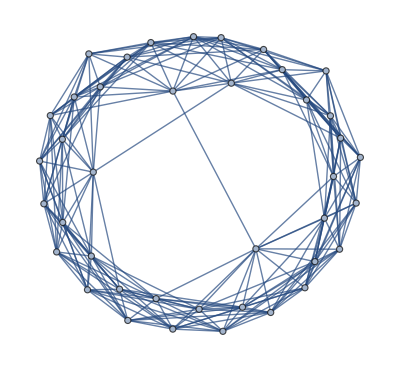
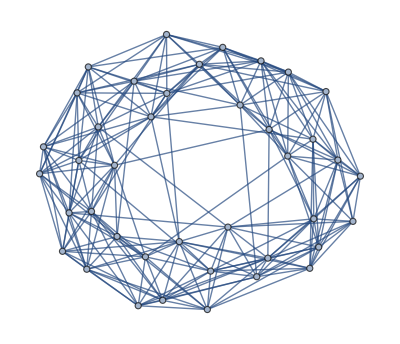
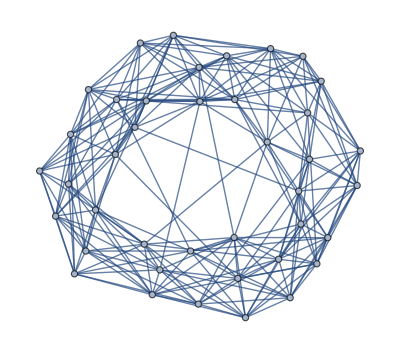
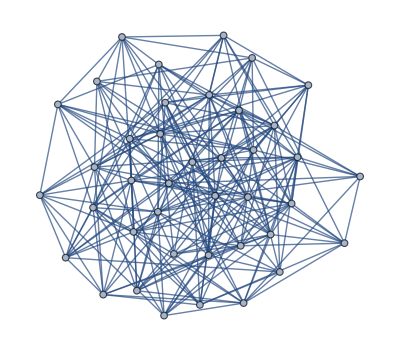
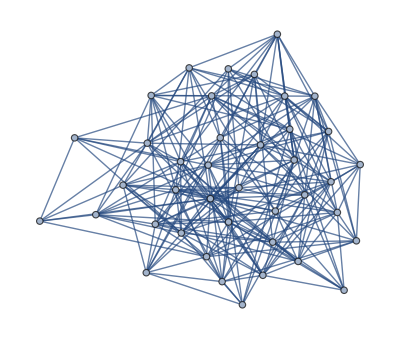

```mathematica
SeedRandom[2222];randomGraphsWattsStrogatz=
RandomGraph[
WattsStrogatzGraphDistribution[40,#,6]]&/@
{0.01,0.02,0.05,0.1,0.5,1}
```

```mathematica
empiricalDistributionsWattsStrogatz=
EmpiricalDistribution[
VertexDegree[#]]&/@randomGraphsWattsStrogatz;
```

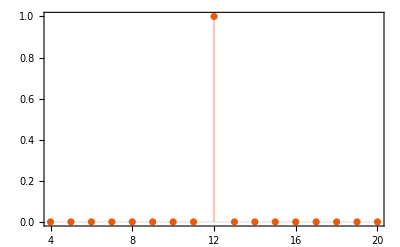
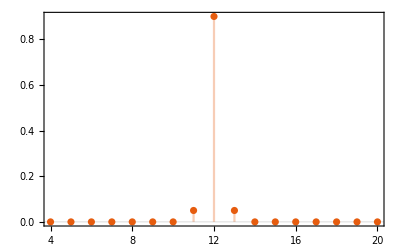
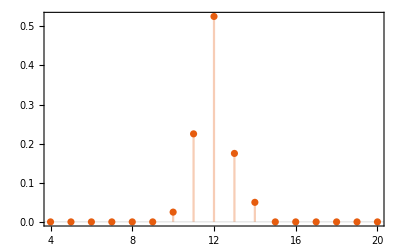
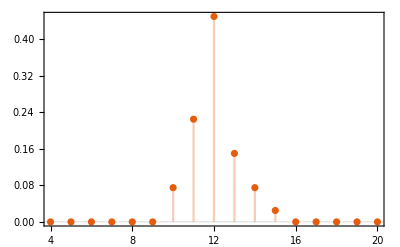
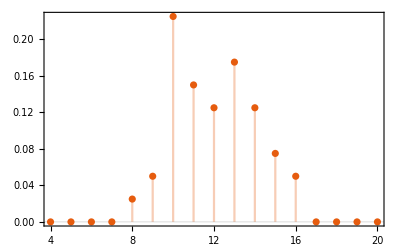
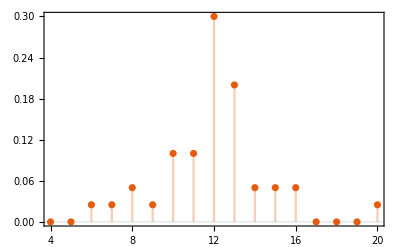

```mathematica
DiscretePlot[PDF[#,i],{i,4,20},
PlotRange-> All,PlotTheme-> "Scientific"]&/@
empiricalDistributionsWattsStrogatz
```